# Converter efficiency with quasi-phase matching

## Six collective modes; symbolic Q; conventions of Abhishek_Converter.nb

Evaluate the notebook from the top. Q is the real magnitude of the normalized overlap of the optical/blue and UV/microwave collective atomic profiles. It remains symbolic until the numerical example at the end. The extra modes pPerp and rPerp retain the orthogonal collective response. This is the uniform-control, homogeneous-linewidth, frozen-position linear model discussed in the accompanying calculation.

The equations preserve the supplied notebook's signs, epsilon, drive Ein, G/Sqrt[2], Gmu/Sqrt[2], and (gammar + kappamu)/2 microwave damping. Omega is the coupling matrix element used in the original file. Rates in the numerical examples use its MHz convention. CellContext is Notebook, so this notebook has its own symbol context.

## Symbolic assumptions and six equations

```mathematica
ClearAll[Evaluate[$Context<>"*"]];
assumptions={G,Gμ,κ,Γ,Δe,Δr,γr,κμ,Δμ,Ω,Ein,ϵ,ω,Q}∈Reals&&G>0&&Gμ>0&&κ>0&&Γ>0&&γr>0&&κμ>0&&Ω>0&&Ein>0&&ϵ>0&&0≤Q≤1;
```

a and b are the optical and microwave cavity amplitudes. p and r are the optically addressed collective optical and Rydberg amplitudes. pPerp and rPerp are the orthogonal pair. The microwave coupling splits into Q Gmu/Sqrt[2] and Sqrt[1-Q^2] Gmu/Sqrt[2]. Detunings are real and may be zero or negative.

```mathematica
equationsQ={ϵ ⅈ ω a==(ϵ ⅈ G p)/(√2)-(κ a)/2+ⅈ ϵ Ein,ϵ ⅈ ω p==(ϵ ⅈ G a)/(√2)+ϵ ⅈ Ω r-(Γ/2-ϵ ⅈ Δe) p,ϵ ⅈ ω r==ϵ ⅈ Ω p-(γr/2-ϵ ⅈ Δr) r+(ϵ ⅈ Gμ Q b)/(√2),ϵ ⅈ ω b==-((γr+κμ)/2-ϵ ⅈ Δμ) b+(ϵ ⅈ Gμ (Q r+√(1-Q^2) rPerp))/(√2),ϵ ⅈ ω rPerp==ϵ ⅈ Ω pPerp-(γr/2-ϵ ⅈ Δr) rPerp+(ϵ ⅈ Gμ √(1-Q^2) b)/(√2),ϵ ⅈ ω pPerp==ϵ ⅈ Ω rPerp-(Γ/2-ϵ ⅈ Δe) pPerp};
variablesQ={a,p,r,b,rPerp,pPerp};
Column[equationsQ,Spacings->1]
```

ⅈ a ϵ ω==ⅈ Ein ϵ+(ⅈ G p ϵ)/(√2)-(a κ)/2
ⅈ p ϵ ω==(ⅈ a G ϵ)/(√2)-p (Γ/2-ⅈ Δe ϵ)+ⅈ r ϵ Ω
ⅈ r ϵ ω==(ⅈ b Gμ Q ϵ)/(√2)-r (γr/2-ⅈ Δr ϵ)+ⅈ p ϵ Ω
ⅈ b ϵ ω==(ⅈ Gμ (Q r+√(1-Q^2) rPerp) ϵ)/(√2)+b (ⅈ Δμ ϵ+1/2 (-γr-κμ))
ⅈ rPerp ϵ ω==(ⅈ b Gμ √(1-Q^2) ϵ)/(√2)-rPerp (γr/2-ⅈ Δr ϵ)+ⅈ pPerp ϵ Ω
ⅈ pPerp ϵ ω==-pPerp (Γ/2-ⅈ Δe ϵ)+ⅈ rPerp ϵ Ω

```mathematica
solutionQ=First[Solve[equationsQ,variablesQ]];
ConverterEfficQFromSolve=√(κμ κ) (b/.solutionQ);
```

## Compact analytical amplitude and orthogonal-mode response

The following factored expression equals the direct Solve result. The definitions include epsilon so that the full symbolic convention of the original notebook is preserved. Eliminating the orthogonal pair adds SigmaPerp to dm; it does not change the useful microwave output-port coupling.

```mathematica
da=κ/2+ⅈ ϵ ω;
de=Γ/2+ⅈ ϵ (ω-Δe);
dr=γr/2+ⅈ ϵ (ω-Δr);
dm=(γr+κμ)/2+ⅈ ϵ (ω-Δμ);
go=(ϵ G)/(√2);
gm=(ϵ Gμ)/(√2);
ob=ϵ Ω;
atomicDen=de dr+ob^2;
opticalFactor=da atomicDen+go^2 dr;
microwaveFactor=dm atomicDen+gm^2 de;
denominatorQ=opticalFactor microwaveFactor+Q^2 go^2 gm^2 ob^2;
ConverterEfficQ=(ϵ Ein √(κμ κ) go gm ob Q atomicDen)/denominatorQ;
SigmaPerp=(gm^2 (1-Q^2) de)/atomicDen;
SigmaPerp
```

(Gμ^2 (1-Q^2) ϵ^2 (Γ/2+ⅈ ϵ (-Δe+ω)))/(2 ((Γ/2+ⅈ ϵ (-Δe+ω)) (γr/2+ⅈ ϵ (-Δr+ω))+ϵ^2 Ω^2))

```mathematica
solveAgreement=TrueQ[FullSimplify[Together[ConverterEfficQFromSolve-ConverterEfficQ]==0,assumptions]];
orthogonalSolution=First[Solve[equationsQ⟦{5,6}⟧,{rPerp,pPerp}]];
sigmaAgreement=TrueQ[FullSimplify[Together[(-(ⅈ gm √(1-Q^2) rPerp)/b/.orthogonalSolution)-SigmaPerp]==0,assumptions]];
Association["Solve equals compact amplitude"->solveAgreement,"Elimination gives SigmaPerp"->sigmaAgreement]
```

<|Solve equals compact amplitude→True,Elimination gives SigmaPerp→True|>

This display uses inert labels for the compact formula; the evaluated expression is stored in ConverterEfficQ. The labels fAtom, yOpt and zMM denote atomicDen, opticalFactor and microwaveFactor; gO, gM and omegaB denote go, gm and ob.

```mathematica
ConverterEfficQ==(ϵ Ein √(κ κμ) gO gM omegaB Q fAtom)/(yOpt zMM+Q^2 gO^2 gM^2 omegaB^2)
```

ConverterEfficQ==(ϵ Ein √(κ κμ) gO gM omegaB Q fAtom)/(yOpt zMM+Q^2 gO^2 gM^2 omegaB^2)

## Efficiency, original-model limit, and projected approximation

EfficiencyQ follows the original definition Abs[ConverterEffic]^2. Because the source keeps Ein explicit, use EfficiencyQ/Ein^2 for an input-amplitude-normalized result. All numerical examples below set Ein = 1. No numerical value of Q has been assigned.

```mathematica
EfficiencyQ=Refine[Abs[ConverterEfficQ]^2,assumptions];
NormalizedEfficiencyQ=EfficiencyQ/Ein^2;
originalEquations=equationsQ⟦1;;4⟧/.{Q->1,rPerp->0,pPerp->0};
originalSolution=First[Solve[originalEquations,{a,b,p,r}]];
ConverterEfficOriginal=√(κμ κ) (b/.originalSolution);
EfficiencyOriginal=Refine[Abs[ConverterEfficOriginal]^2,assumptions];
ConverterEfficProjected=ConverterEfficOriginal/.Gμ->Q Gμ;
EfficiencyProjected=Refine[Abs[ConverterEfficProjected]^2,assumptions];
originalLimitCheck=TrueQ[FullSimplify[Together[(ConverterEfficQ/.Q->1)-ConverterEfficOriginal]==0,assumptions]];
zeroOverlapCheck=TrueQ[FullSimplify[ConverterEfficQ/.Q->0,assumptions]==0];
Association["Q = 1 recovers uploaded model"->originalLimitCheck,"Q = 0 gives zero conversion"->zeroOverlapCheck]
```

<|Q = 1 recovers uploaded model→True,Q = 0 gives zero conversion→True|>

EfficiencyProjected implements only Gmu -> Q Gmu. EfficiencyQ also retains the orthogonal atomic response. These are two different models; multiplying the original efficiency by Q^2 is not equivalent to either one.

## Zero detunings and analytical on-resonance expression

```mathematica
simplifications={Δe->0,Δr->0,Δμ->0,Ein->1,ϵ->1};
SimpleConverterQ=Together[ConverterEfficQ/.simplifications];
SimpleEfficiencyQ=Refine[Abs[SimpleConverterQ]^2,assumptions];
OnResonanceEfficiencyQ=FullSimplify[SimpleEfficiencyQ/.ω->0,assumptions];
OnResonanceEfficiencyQ
```

(64 G^2 Gμ^2 Q^2 κ κμ Ω^2 (Γ γr+4 Ω^2)^2)/((κ (Γ γr+4 Ω^2) (2 Gμ^2 Γ+(γr+κμ) (Γ γr+4 Ω^2))+2 G^2 (γr (γr+κμ) (Γ γr+4 Ω^2)+2 Gμ^2 (Γ γr+4 Q^2 Ω^2)))^2)

```mathematica
cooperativityRules={cO->(2 G^2)/(κ Γ),cM->(2 Gμ^2)/((κμ+γr) γr),cB->(4 Ω^2)/(Γ γr)};
EfficiencyCooperativities=(κμ 4 Q^2 cO cM cB (1+cB)^2)/((κμ+γr) ((1+cB+cO) (1+cB+cM)+Q^2 cO cM cB)^2);
cooperativityCheck=TrueQ[FullSimplify[Together[OnResonanceEfficiencyQ-(EfficiencyCooperativities/.cooperativityRules)]==0,assumptions]];
{{EfficiencyCooperativities}, {"Agrees with the six-equation result: "<>ToString[cooperativityCheck]}}
```

(4 cB (1+cB)^2 cM cO Q^2 κμ)/(((1+cB+cM) (1+cB+cO)+cB cM cO Q^2)^2 (γr+κμ))
Agrees with the six-equation result: True

```mathematica
ExtraMicrowaveLinewidth=FullSimplify[2 Re[SigmaPerp/.simplifications/.ω->0],assumptions];
ExtraMicrowaveLinewidth
```

-(2 Gμ^2 (-1+Q^2) Γ)/(Γ γr+4 Ω^2)

ExtraMicrowaveLinewidth is the additional full effective microwave linewidth on resonance. At nonzero detuning use the complex SigmaPerp, not a constant broadening. The output-port factor in the numerator remains fixed.

## Additional cavity-port losses

```mathematica
EfficiencyQWithPorts=etaOpt etaMM EfficiencyQ;
```

etaOpt and etaMM are additional desired-port fractions multiplying the original notebook result at fixed total cavity linewidths. They are set to one below. If changing mirror/port coupling also changes the linewidths, update kappa and kappamu consistently; the port factors alone do not describe that redesign.

## Symbolic validation

```mathematica
validation=Association["Direct Solve = compact expression"->solveAgreement,"Orthogonal elimination = SigmaPerp"->sigmaAgreement,"Q = 1 = original notebook"->originalLimitCheck,"Q = 0 = zero conversion"->zeroOverlapCheck,"On-resonance cooperativity formula"->cooperativityCheck];
validation
```

<|Direct Solve = compact expression→True,Orthogonal elimination = SigmaPerp→True,Q = 1 = original notebook→True,Q = 0 = zero conversion→True,On-resonance cooperativity formula→True|>

The extra collective-mode closure assumes uniform control and atomic linewidths. It does not separately resolve motional sidebands, inhomogeneous light shifts, blockade, or additional independent standing-wave channels. The example Q also assumes perpendicular UV and exact matching to the chosen reciprocal-lattice vectors. Efficiency denotes coherent signal conversion, not a noise or fidelity calculation.

## Numerical example: choose parameters, then substitute Q

The original notebook parameter set is preserved as parmsOriginal. parmsScreenshot reproduces the previously supplied 82.094% screenshot (the exact resonance value is 82.0957%; its 1000-point grid does not sample zero). Select either preset below. Numerical rates are in MHz, as in the supplied notebook.

```mathematica
gopt=0.025;
gmm=0.091;
Natoms=5 10^5;
ΩUV=0.03;
ΔUV=1;
θUV=ArcTan[Abs[ΩUV/ΔUV]];
Nmm=Natoms Sin[θUV]^2;
Nopt=Natoms Cos[θUV]^2;
Gopt=gopt √Nopt;
Gmm=gmm √Nmm;
γopt=6;
γmm=0.1;
κopt=10;
κmm=10;
Ωb=1.45/2;
FBlue=100;
parmsOriginal={G->Gopt,Gμ->Gmm,κ->κopt,Γ->γopt,Δe->0,Δr->0,γr->γmm,κμ->κmm,Δμ->0,Ω->√(FBlue/π) Ωb,Ein->1,ϵ->1};
parmsScreenshot={G->15.847456497032729,Gμ->2.0917014542834487,κ->10.,Γ->6.,Δe->0,Δr->0,γr->0.1,κμ->5.,Δμ->0,Ω->5.524973392693388,Ein->1,ϵ->1};
parameterSet="Screenshot";
parms=Switch[parameterSet,"Original notebook",parmsOriginal,"Screenshot",parmsScreenshot];
portRules={etaOpt->1.,etaMM->1.};
```

The lattice calculation assumes two independent perpendicular second-order-QPM axes with equal depths. The user-specified calibration is U/kB = 5 microkelvin per watt per axis per beam; the waist is 200 micrometres. Temperature zero here is the harmonic lowest-band limit, which still includes zero-point spatial motion.

```mathematica
planckH=6.62607015/10^34;
boltzmannK=1.380649/10^23;
rb85Mass=(84.9117897379 1.6605390666)/10^27;
latticeWavelength=1188/10^9;
recoilUK=(planckH^2 10^6)/(2 rb85Mass latticeWavelength^2 boltzmannK);
latticeWaistUM=200;
latticePowerPerBeam=3.;
latticeDepthUK=5 latticePowerPerBeam;
temperatureUK=0.;
b2[depth_?NumericQ,temp_?NumericQ]:=Exp[-4 √(recoilUK/depth) If[temp==0,1,Coth[(√(depth recoilUK))/temp]]];
b2x=b2[latticeDepthUK,temperatureUK];
b2z=b2[latticeDepthUK,temperatureUK];
qValue=b2x b2z;
qRule={Q->qValue};
Association["b2 per axis"->b2x,"Q = b2x b2z"->qValue,"Q squared"->qValue^2]
```

<|b2 per axis→0.746816,Q = b2x b2z→0.557734,Q squared→0.311067|>

```mathematica
numericalSummary={{"Parameter set",parameterSet},{"Q",qValue},{"Original, on resonance (%)",100 N[EfficiencyOriginal/.parms/.ω->0]},{"Q Gmu only, on resonance (%)",100 N[EfficiencyProjected/.parms/.qRule/.ω->0]},{"Six modes, on resonance (%)",100 N[EfficiencyQ/.parms/.qRule/.ω->0]},{"Six modes with port fractions (%)",100 N[EfficiencyQWithPorts/.parms/.qRule/.portRules/.ω->0]},{"Extra full microwave linewidth (MHz)",N[ExtraMicrowaveLinewidth/.parms/.qRule]}};
Grid[numericalSummary,Frame->All,Alignment->Left,Background->{None,{Lighter[Gray,0.95],White}},Spacings->{2,1}]
```

Parameter set | Screenshot
Q | 0.557734
Original, on resonance (%) | 82.0957
Q Gmu only, on resonance (%) | 51.5929
Six modes, on resonance (%) | 47.0824
Six modes with port fractions (%) | 47.0824
Extra full microwave linewidth (MHz) | 0.294787

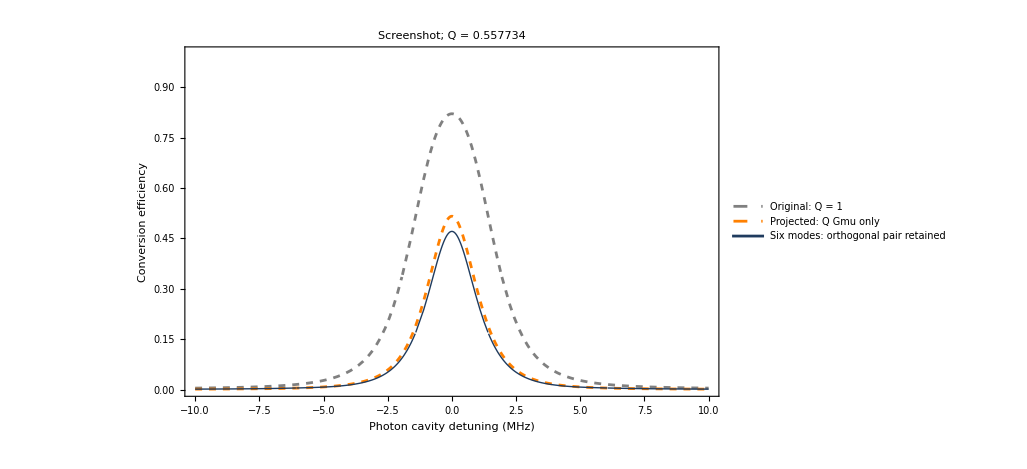

```mathematica
comparisonPlot=Plot[Evaluate[{EfficiencyOriginal,EfficiencyProjected,EfficiencyQ}/.parms/.qRule],{ω,-10,10},PlotRange->{0,1},Frame->True,FrameLabel->{"Photon cavity detuning (MHz)","Conversion efficiency"},PlotLegends->{"Original: Q = 1","Projected: Q Gmu only","Six modes: orthogonal pair retained"},PlotStyle->{{Gray,Dashed},{Orange,Dashed},{RGBColor[0.12, 0.23, 0.37],Thick}},PlotLabel->parameterSet"; Q = "qValue,ImageSize->760,PlotPoints->120,MaxRecursion->4];
comparisonPlot
```

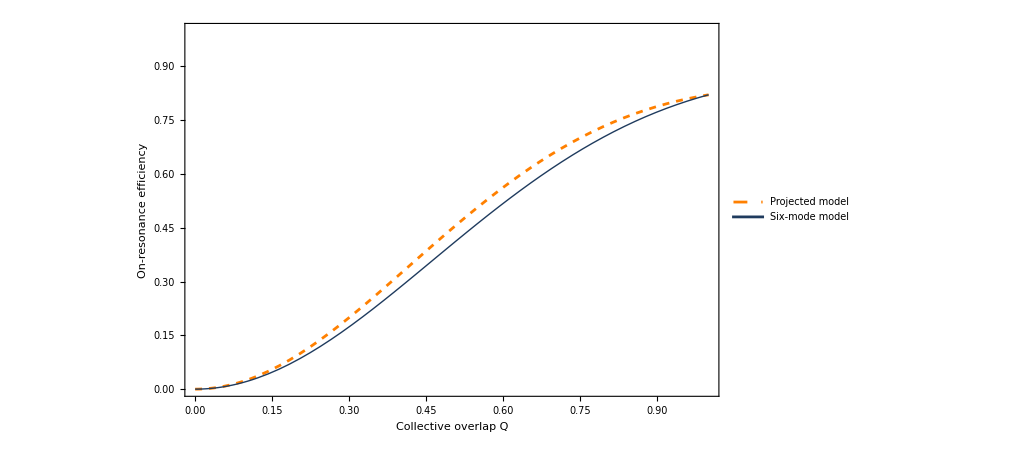

```mathematica
overlapPlot=Plot[Evaluate[{EfficiencyProjected,EfficiencyQ}/.parms/.ω->0],{Q,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"Collective overlap Q","On-resonance efficiency"},PlotLegends->{"Projected model","Six-mode model"},PlotStyle->{{Orange,Dashed},{RGBColor[0.12, 0.23, 0.37],Thick}},ImageSize->760];
overlapPlot
```